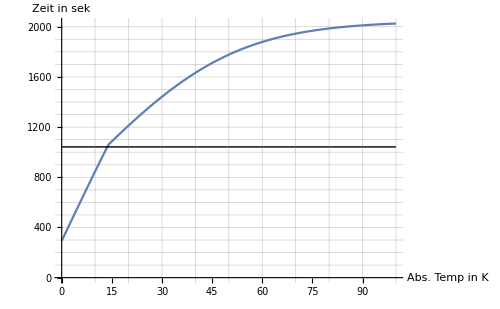

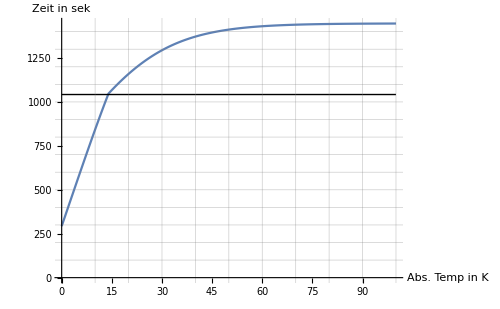

```mathematica
data = Import[FileNameJoin[{NotebookDirectory[],"TempGraph.txt"}], "Data"];
dataalt = Import[FileNameJoin[{NotebookDirectory[],"TempGraph_alt.txt"}], "Data"];
ListLinePlot[data, GridLines->{Table[10*i, {i,0,Ceiling[Max[data[[All,1]]]/10]}],Table[100*i, {i,0,Ceiling[Max[data[[All,2]]]/100]}]},PlotRange->All, AxesLabel->{"Abs. Temp in K","Zeit in sek"},ImageSize->500, Epilog->{Line[{{0, 1042.15},{Ceiling[Max[data[[All,1]]]],1042.15}}]}]
ListLinePlot[dataalt, GridLines->{Table[10*i, {i,0,Ceiling[Max[dataalt[[All,1]]]/10]}],Table[100*i, {i,0,Ceiling[Max[dataalt[[All,2]]]/100]}]},PlotRange->All, AxesLabel->{"Abs. Temp in K","Zeit in sek"},ImageSize->500, Epilog->{Line[{{0, 1042.15},{Ceiling[Max[dataalt[[All,1]]]],1042.15}}]}]
```